{140→23}

Part::pspec: Part specification "140" is neither a machine-sized integer nor a list of machine-sized integers.

{140→23}⟦140⟧

23

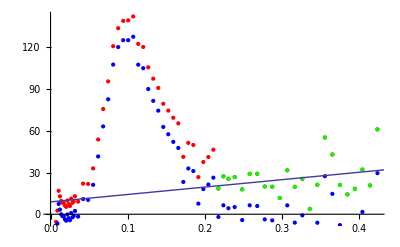

{8.88877+53.2782 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 53.2782 | 41.6721 | 1.27851 | 0.215019
b | 8.88877 | 13.4815 | 0.659334 | 0.516847}

```mathematica
prefix = "PET-";
sample = "140";
path = ParentDirectory[NotebookDirectory[]] <> "/data/" <> prefix <> sample;
rawData=Import[path<>".0.phg","Table"];

data = Take[rawData, -(Length[rawData]-7)];

toRel[array_] := {array[[1]]/(2*Pi) * 10, array[[2]]*(array[[1]] /(2*Pi))^2 * 100};
rel = Map[toRel, data];

sampleSize = 23
notSample = Length[data ] - sampleSize;

linearData =  Take[rel, -sampleSize];
nonLinearData = Take[rel, Length[data ] - sampleSize];
lFit = NonlinearModelFit[linearData,a x + b,{a,b},{x}];

correct[a_] := {a[[1]], a[[2]]-lFit["Function"][a[[1]]]}
correctedRel = Map[correct, rel];


Show[ListPlot[rel,PlotStyle->Red], ListPlot[correctedRel,PlotStyle->Blue], ListPlot[linearData,PlotStyle->Green],Plot[{lFit["BestFit"]},{x,0,0.44}]]

lFit[{"BestFit","ParameterTable"}]

switch[a_] := {a[[2]], a[[1]]}
correctedRelOutput = Map[switch, correctedRel];

Export[path<>".rel", correctedRel, "Table"];
Export[path <> ".fit", lFit["BestFit"], "String"];
Export[path<>"-fitPoints.rel", linearData, "Table"];
Export[path<>"-nonFitPoints.rel", nonLinearData, "Table"];
```